```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]]
```

/Users/tazz/Documents/Git/StabilityProject2014

Plots of Freedonia, Merika, and Kleptopia for low initial dissent.

```mathematica
Freedonia =Import["dataFreedonia.mx"] // Dataset;
Merika =Import["dataMerika.mx"] // Dataset;
Kleptopia=Import["dataKleptopia.mx"]//Dataset;
ListLinePlot[{{Freedonia},{Merika},{Kleptopia}},PlotRange->Automatic,PlotLegends->{"Freedonia","Merika","Kleptopia"},PlotStyle->{Green,Blue,Red}]
```

-Graphics-

```mathematica
TableForm[Freedonia]
```

{ { 0,3.9586×10^-2,6.3×10^7,⋯_2 },{ 1,3.5574×10^-2,3.6108×10^7,⋯_2 } }
2 levels | 2rowsDataset[{__List}]

New lines to convert Scientific form to plotable form:

```mathematica
Freedonia = Freedonia/.ScientificForm[n_,rest___]->n
Merika = Merika/.ScientificForm[n_,rest___]->n
Kleptopia = Kleptopia/.ScientificForm[n_,rest___]->n
```

0. | 0.03959 | 6.3×10^7 | 2.87×10^8 | 1.605×10^1355718576299609
1. | 0.03557 | 3.611×10^7 | 3.139×10^8 | 0.004011
2 levels | 2rows |  |  |  | Dataset[{__List}]

0. | 0.04573 | 9.1×10^7 | 2.59×10^8 | 1.605×10^1355718576299609
1. | 0.04188 | 7.096×10^7 | 2.79×10^8 | 0.003854
2 levels | 2rows |  |  |  | Dataset[{__List}]

0. | 1.069 | 4.1×10^7 | 9.×10^6 | 1.605×10^1355718576299609
1. | 1.072 | 4.072×10^7 | 9.276×10^6 | 0.002852
2 levels | 2rows |  |  |  | Dataset[{__List}]

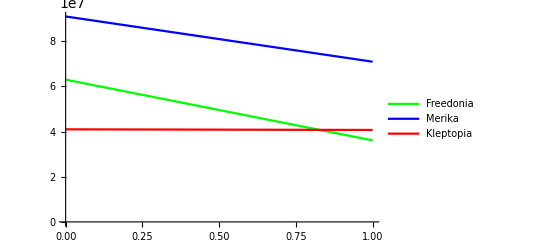

```mathematica
ListLinePlot[{Freedonia[All,{1,3}]//Normal,Merika[All,{1,3}]//Normal,Kleptopia[All,{1,3}] //Normal },PlotLegends->{"Freedonia","Merika","Kleptopia"},PlotStyle->{Green,Blue,Red}]
```